```mathematica
data = SemanticImport[NotebookDirectory[]<>"/dataset/a1_raw.csv"]
```

Dataset[<>]

```mathematica
test = SemanticImport[NotebookDirectory[]<>"/dataset/a2_raw.csv"]
```

Dataset[<>]

```mathematica
validModel=Table[Table[test[[n,x]],{x,18}]->test[[n,19]],{n,1,Length[test]/2}]
```

{{4.49608,5.58357,1.68939,6.93239,5.43292,1.65058,5.53213,1.4734,1.78244,5.57917,4.10922,1.77759,4.50342,5.20035,1.70377,6.61575,5.20614,1.65457}→E,{4.49673,5.54779,1.69004,6.9338,5.40858,1.65262,5.53213,1.47315,1.78191,5.57993,4.10931,1.77737,4.50467,5.16318,1.70291,6.61751,5.18119,1.65654}→E,{4.49595,5.52541,1.69031,6.93265,5.43424,1.65016,5.53182,1.4727,1.7819,5.58053,4.10937,1.77707,4.50036,5.14064,1.70309,6.61644,5.20664,1.65394}→E,{4.49961,5.59921,1.68636,6.97294,5.38931,1.65691,5.53257,1.47276,1.78169,5.58115,4.11135,1.77661,4.55507,5.21314,1.68799,6.61082,5.24435,1.65549}→E,{4.49723,5.59836,1.68468,6.93271,5.42,1.64814,5.53278,1.47296,1.78143,5.5813,4.1109,1.77641,4.5501,5.2122,1.68815,6.62165,5.18476,1.65033}→E,623,{5.43874,3.53379,1.40344,5.62627,3.63354,1.37665,5.3643,1.46029,1.74362,5.51223,4.23693,1.73254,5.18103,3.59754,1.46199,5.87221,3.62497,1.41523}→G,{5.38686,3.57854,1.41163,5.52689,3.54468,1.35542,5.36544,1.47051,1.74368,5.51269,4.24526,1.73225,5.14836,3.63736,1.46756,5.77082,3.57348,1.39412}→G,{5.49631,3.52451,1.37736,5.5115,3.58414,1.36063,5.36091,1.47695,1.74262,5.5059,4.28524,1.7327,5.23157,3.59826,1.44169,5.75858,3.60319,1.39877}→G,{5.41589,3.33781,1.37575,4.83005,3.57143,1.45082,5.35537,1.48003,1.74134,5.50534,4.2869,1.73276,5.17126,3.45832,1.44043,5.24271,3.58889,1.46912}→G}
 |  |  |  |

```mathematica
Options[Classify]
```

{Method→Automatic,PerformanceGoal→Automatic,NominalVariables→Automatic,ValidationSet→None,FeatureNames→Automatic,FeatureTypes→Automatic,IndeterminateThreshold→Automatic,UtilityFunction→Automatic,Weights→Automatic,RandomSeeding→Automatic,FeatureWeights→Automatic,DistributionPostProcessing→Automatic,PredictionName→Automatic,RecordLog→True,FeatureExtractor→Identity,ImputeMissingValues→True,ProcessorCaching→True,BatchProcessing→Automatic,MinimalPreprocessing→False,ClassPriors→Automatic,TieBreakerFunction→RandomChoice}

```mathematica
c = Classify[data -> "phase", Method-> {"SupportVectorMachine", "KernelType"->"Polynomial"}]
```

ClassifierFunction[…]

```mathematica
testModel = Table[Table[test[[n,x]], {x, 18}] -> test[[n,19]], {n, Length[test]/2, Length[test]}]
```

{{5.41589,3.33781,1.37575,4.83005,3.57143,1.45082,5.35537,1.48003,1.74134,5.50534,4.2869,1.73276,5.17126,3.45832,1.44043,5.24271,3.58889,1.46912}→G,{5.41087,3.29381,1.37815,4.85251,3.41916,1.44401,5.34883,1.47632,1.74007,5.50545,4.28538,1.73284,5.16633,3.42402,1.44209,5.25505,3.46532,1.46833}→G,629,{3.79464,5.24589,1.62886,6.73562,5.14287,1.50775,5.46974,1.40993,1.69296,5.35615,4.15235,1.69915,4.15541,5.07669,1.62341,6.63255,4.91689,1.53967}→G,{3.81556,5.27971,1.63865,6.69994,5.18475,1.51443,5.48009,1.41095,1.69415,5.34333,4.15154,1.69874,4.16996,5.11435,1.62241,6.61583,4.94208,1.54355}→G}
 |  |  |  |

```mathematica
cm = ClassifierMeasurements[c, testModel]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Properties"]
```

{Accuracy,AccuracyRejectionPlot,AreaUnderROCCurve,BestClassifiedExamples,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,CorrectlyClassifiedExamples,DecisionUtilities,Error,Examples,F1Score,FalseDiscoveryRate,FalseNegativeExamples,FalseNegativeRate,FalsePositiveExamples,FalsePositiveRate,GeometricMeanProbability,IndeterminateExamples,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,MisclassifiedExamples,MostCertainExamples,NegativePredictedValue,Perplexity,Precision,Probabilities,ProbabilityHistogram,Properties,Recall,RejectionRate,ROCCurve,ScottPi,Specificity,TopConfusions,TrueNegativeExamples,TruePositiveExamples,WorstClassifiedExamples}

```mathematica
cm["Precision"]
```

<|E→0.455526,G→0.900763|>

```mathematica
cm["Accuracy"]
```

0.63981

```mathematica
xy = DimensionReduce[data]
```

{{-1.90433,-1.91787},{-1.59588,-2.76979},{-2.00345,-2.39933},{-1.77412,-2.54215},{-1.86675,-2.46984},{-1.92363,-2.38771},{-1.94985,-2.38081},{-1.95996,-2.36593},{-1.97119,-2.35588},{-1.97729,-2.37436},1728,{-1.89261,-2.96828},{-1.87741,-2.99427},{-1.73685,-3.15311},{-1.72081,-3.22015},{-1.73063,-3.18666},{-1.90156,-3.00329},{-1.89252,-3.03777},{-1.91131,-3.00151},{-1.75194,-3.177}}
 |  |  |  |

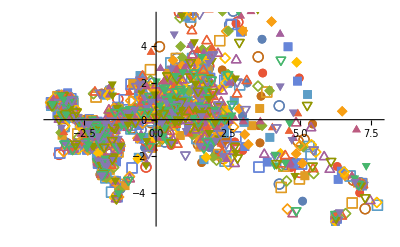

```mathematica
ListPlot[List/@xy,PlotMarkers->Automatic]
```

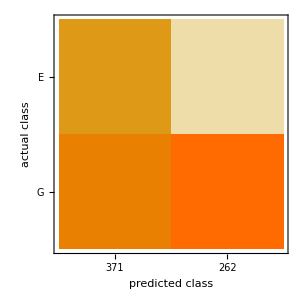

```mathematica
cm["ConfusionMatrixPlot"]
```

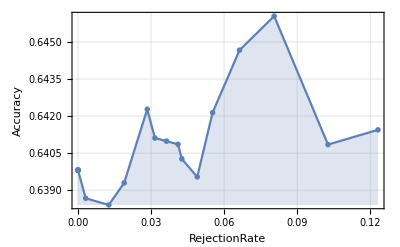

```mathematica
cm["AccuracyRejectionPlot"]
```

```mathematica
loss[{c_,gamma_,b_,d_}]:=-ClassifierMeasurements[Classify[data -> "phase",Method->{"SupportVectorMachine","KernelType"->"Polynomial","SoftMarginParameter"->Exp[c],"GammaScalingParameter"->Exp[gamma],"BiasParameter"->Exp[b],"PolynomialDegree"->d}],validModel,"LogLikelihoodRate"];
```

```mathematica
region=ImplicitRegion[And[-3.≤c≤3.,-3.≤gamma≤3.,-1.≤b≤2.,1≤d≤3,d∈Integers],{c,gamma,b,d}]
```

ImplicitRegion[-3.≤c≤3.&&-3.≤gamma≤3.&&-1.≤b≤2.&&1≤d≤3&&d∈Integers,{c,gamma,b,d}]

```mathematica
bmo=BayesianMinimization[loss,region]
```

BayesianMinimizationObject[…]

```mathematica
bmo["MinimumConfiguration"]
```

{-1.56197,-2.72262,0.0136116,1}

```mathematica
bmo["EvaluationHistory"]
```

Dataset[<>]

```mathematica
c2 =Classify [data -> "phase"  ,
Method->{"SupportVectorMachine",
"KernelType"->"Polynomial",
"SoftMarginParameter"->Exp[0.4935391554689126],
"GammaScalingParameter"->Exp[1.7422739911787666],
"BiasParameter"->Exp[-0.8998692403216122],
"PolynomialDegree"->1}]
```

Classify::mlbddata: The data is not formatted correctly.

Classify[Dataset[<>]→phase Method→{SupportVectorMachine,KernelType→Polynomial,SoftMarginParameter→1.6381,GammaScalingParameter→5.71031,BiasParameter→0.406623,PolynomialDegree→1}]

```mathematica
cm2 = ClassifierMeasurements[c2, testModel]
```

Classify::mlbddata: The data is not formatted correctly.

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of Classify[Dataset[«1747»]→phase Method→{SupportVectorMachine,KernelType→Polynomial,SoftMarginParameter→1.6381,GammaScalingParameter→5.71031,BiasParameter→0.406623,PolynomialDegree→1}].

ClassifierMeasurements[Classify[Dataset[<>]→phase Method→{SupportVectorMachine,KernelType→Polynomial,SoftMarginParameter→1.6381,GammaScalingParameter→5.71031,BiasParameter→0.406623,PolynomialDegree→1}],{{5.41589,3.33781,1.37575,4.83005,3.57143,1.45082,5.35537,1.48003,1.74134,5.50534,4.2869,1.73276,5.17126,3.45832,1.44043,5.24271,3.58889,1.46912}→G,631,{3.81556,5.27971,1.63865,6.69994,5.18475,1.51443,5.48009,1.41095,1.69415,5.34333,4.15154,1.69874,4.16996,5.11435,1.62241,6.61583,4.94208,1.54355}→G}]
 |  |  |  |

```mathematica
cm2["Accuracy"]
```

ClassifierMeasurements[Classify[Dataset[<>]→phase Method→{SupportVectorMachine,KernelType→Polynomial,SoftMarginParameter→1.6381,GammaScalingParameter→5.71031,BiasParameter→0.406623,PolynomialDegree→1}],{{5.41589,3.33781,1.37575,4.83005,3.57143,1.45082,5.35537,1.48003,1.74134,5.50534,4.2869,1.73276,5.17126,3.45832,1.44043,5.24271,3.58889,1.46912}→G,{5.41087,3.29381,1.37815,4.85251,3.41916,1.44401,5.34883,1.47632,1.74007,5.50545,4.28538,1.73284,5.16633,3.42402,1.44209,5.25505,3.46532,1.46833}→G,630,{3.81556,5.27971,1.63865,6.69994,5.18475,1.51443,5.48009,1.41095,1.69415,5.34333,4.15154,1.69874,4.16996,5.11435,1.62241,6.61583,4.94208,1.54355}→G}][Accuracy]
 |  |  |  |

```mathematica
func[method_]:=-ClassifierMeasurements[Classify[data->"Phase",Method->method],testModel,"LogLikelihood"];
methods={"NearestNeighbors","NeuralNetwork","SupportVectorMachine"};
```

```mathematica
bo=BayesianMinimization[func,methods]
```

Part::partw: Part 1 of <||> does not exist.

Classify::mlbddata: The data is not formatted correctly.

Classify::mlwcol: Unknown variable index Phase. The index of the output variable should a be string or an integer.

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of Classify[Dataset[«1747»]→Phase,Method→NearestNeighbors].

BayesianMinimization::bdfnconfig: The function should be real valued.

BayesianMinimization[func,{NearestNeighbors,NeuralNetwork,SupportVectorMachine}]

```mathematica
bo["EvaluationHistory"]
```

BayesianMinimization[func,{NearestNeighbors,NeuralNetwork,SupportVectorMachine}][EvaluationHistory]

```mathematica
bo["MinimumValue"]
```

BayesianMinimization[func,{NearestNeighbors,NeuralNetwork,SupportVectorMachine}][MinimumValue]

```mathematica
ListPlot[data[;;10]]
```

-Graphics-